## Цель работы

Изучить градиентные методы решения задачи нелинейного программирования.

## Исходные данные

ЭВС состоит из двух блоков: процессорного и цифро-аналогового. Вероятности отказа блоков за заданную наработку равны q1 и q2. Потребляемая мощность p1 и p2 . Требуется найти оптимальный резерв для каждого из блоков для заданной общей вероятности отказов не более q0  и минимальной потребляемой мощности. Резерв должен быть нагруженным.

```mathematica
q0 = 0.002;
q1 = 0.05;
q2 = 0.02;
p1 = 3; (*Вт*)
p2 = 5; (*Вт*)
```

Целевая функция

```mathematica
TargetF:=p1*(x1+1) + p2*(x2+1);
```

Ограничение

```mathematica
QRestriction:=q1^(x1+1)+q2^(x2+1);
```

### Используемые формулы для вычислений

```mathematica
EvaluateRestriction[x1_, x2_]:=q1^(x1+1)+q2^(x2+1);
GradQ:=Grad[QRestriction, {x1,x2}];
EvaluateGradQ1[value1_]:=Assuming[x1==value1,Refine[GradQ[[1]]]];
EvaluateGradQ2[value2_]:=Assuming[x2==value2,Refine[GradQ[[2]]]];
AbsGradQ[x1_,x2_]:=Sqrt[EvaluateGradQ1[x1]^2+EvaluateGradQ2[x2]^2];
EvaluateTargetF[x1_, x2_]:=p1*(x1+1) + p2*(x2+1);
GradTargetF:=Grad[TargetF, {x1,x2}];
EvaluateGradTarget1[value1_]:=Assuming[x1==value1,Refine[GradTargetF[[1]]]];
EvaluateGradTarget2[value2_]:=Assuming[x2==value2,Refine[GradTargetF[[2]]]];
AbsGradF[x1_,x2_]:=Sqrt[EvaluateGradTarget1[x1]^2+EvaluateGradTarget2[x2]^2];
```

### Функции вывода графиков

```mathematica
PlotAllowedPoints[x1_,x2_]:=Module[{i=0,j=0,array = {{0,0}}},
For[i=0,i≤x1,i++,For[j=0,j≤x2,j++,AppendTo[array,{i,j}];];];
ListPlot[array, PlotStyle->Black]];
PlotRestrictionArea[max1_,max2_]:=RegionPlot[QRestriction≤q0,{x1,0,max1},{x2,0,max2},PlotLegends->{QRestriction}, AxesLabel->Automatic, PlotStyle->LightGray,BoundaryStyle->LightGray];
PlotAllowedArea[max1_,max2_]:=Show[PlotRestrictionArea[max1,max2],PlotAllowedPoints[max1,max2]];
PointsLength[x1_,y1_,x2_,y2_]:=Sqrt[(x2-x1)^2+(y2-y1)^2];
```

## Ход работы

### Решение задачи градиентным методом с дроблением шага

Т.к. в задаче присутствует ограничение по вероятности отказа системы, необходимо добавить условие для проверки ограничения. В случае не выполнения ограничения, движение производится в направлении, противоположном направлению градиента функции суммарной вероятности отказа системы.

```mathematica
FindNextPoint[cur1_,cur2_,step_]:=Module[{grad1,grad2,new1,new2},
If[EvaluateRestriction[cur1,cur2]≤q0,
grad1=EvaluateGradTarget1[cur1];
grad2=EvaluateGradTarget2[cur2];,
grad1=EvaluateGradQ1[cur1];
grad2=EvaluateGradQ2[cur2];
];
new1=cur1-grad1*step;
new2=cur2-grad2*step;
Return[{new1,new2}];
];
```

Для решения задачи используется градиентный метод с дроблением параметра шага:
λ_k+1 = λ_k / √k.

```mathematica
FindMinSplit[init1_,init2_,initStep_,ϵ_]:=Module[{k=1,cur1=init1,cur2=init2,curF,nextPoint,array,step,prevF, func},
step=initStep;
curF=EvaluateTargetF[init1,init2];
nextPoint=FindNextPoint[init1,init2,step];
array={{init1,init2}};
While[Abs[cur1-nextPoint[[1]]]≥ϵ||Abs[cur2-nextPoint[[2]]]≥ϵ,
prevF=EvaluateTargetF[cur1,cur2];
cur1=nextPoint[[1]];
cur2=nextPoint[[2]];
curF=EvaluateTargetF[cur1,cur2];
AppendTo[array,{cur1,cur2}];
nextPoint=FindNextPoint[cur1,cur2,step];
k++;
If[curF>prevF,step=initStep/Sqrt[k]];
];
PrintResult[k,init1,init2,cur1,cur2];
func=Show[ListPlot[array,PlotRange->{{0,3},{0,3}},PlotStyle->Orange],ListPlot[{{array[[1]][[1]],array[[1]][[2]]}},PlotStyle->Green,PlotMarkers->"●"],
ListPlot[{{Last[array][[1]],Last[array][[2]]}},PlotStyle->Red,PlotMarkers->"●"]];
Show[PlotAllowedArea[3,3],func]
];
```

Для использования градиентоного метода, предполагаем, что искомые величины непрерывные. После оптимизации из ближайших целочисленных значений выбирается лучшее решение по значению целевой функции и выполнению ограничения.

```mathematica
PrintResult[k_,init1_,init2_, x1_,x2_]:=Module[{ceil1=Ceiling[x1],ceil2=Ceiling[x2],floor1=Floor[x1],floor2=Floor[x2],ans1=-1,ans2=-1},
Module[{p1,p2,p3,p4,l, ansL},
p1={ceil1,ceil2};
p2:={ceil1,floor2};
p3:={floor1,floor2};
p4={floor1,ceil1};
l:={PointsLength[x1,x2,p1[[1]],p1[[2]]],PointsLength[x1,x2,p2[[1]],p2[[2]]],PointsLength[x1,x2,p3[[1]],p3[[2]]],PointsLength[x1,x2,p4[[1]],p4[[2]]]};
ansL=l[[1]];
If[EvaluateRestriction[p1[[1]], p1[[2]]]≤q0,
ans1=p1[[1]];
ans2=p1[[2]];,
If[EvaluateRestriction[p2[[1]], p2[[2]]]≤q0&&l[[2]]<ansL,
ansL=l[[2]];
ans1=p2[[1]];
ans2=p2[[2]];,
If[EvaluateRestriction[p3[[1]], p3[[2]]]≤q0&&l[[3]]<ansL,
ansL=l[[3]];
ans1=p3[[1]];
ans2=p3[[2]];,
If[EvaluateRestriction[p4[[1]], p4[[2]]]≤q0&&l[[4]]<ansL,
ansL=l[[4]];
ans1=p4[[1]];
ans2=p4[[2]];
];];];];];
Print[Row[{"Количество итераций",k},"="]];
Print["Исходный резерв:"];
Print[Row[{" процессорного блока",Row[{1,init1},"+"]},"="]];
Print[Row[{" цифро-аналогового блока",Row[{1,init2},"+"]},"="]];
If[ans1==-1||ans2==-1,Print["Failed"],
Print["Необходимое изменение резерва:"];
Print[Row[{" процессорного блока",x1-init1},"="]];
Print[Row[{" цифро-аналогового блока",x2-init2},"="]];
Print["Итоговый резерв:"];
Print[Row[{" процессорного блока",Row[{x1,ans1},"→"]},"="]];
Print[Row[{" цифро-аналогового блока",Row[{x2,ans2},"→"]},"="]];
Print[Row[{"Вероятность отказа системы",EvaluateRestriction[ans1,ans2]},"="]];
Print[Row[{"Потребляемая мощность системы",EvaluateTargetF[ans1,ans2]},"="]];];
];
```

### Примеры решения задачи при различных стартовых точках

Начальная величина шага

```mathematica
λ=0.05;
```

Константа остановки

```mathematica
ϵ=0.000001;
```

Зеленой точкой отмечена стартовая точка, красной - финальная точка. ОДР представлена серой областью, а разрешенные (целочисленные) значения - черными точками.

#### Старт из области, где выполняется ограничение

==Количество итераций108538

Исходный резерв:

== процессорного блока++12.5

== цифро-аналогового блока++11.8

Необходимое изменение резерва:

== процессорного блока-0.811391

== цифро-аналогового блока-1.16749

Итоговый резерв:

== процессорного блока→→1.688612

== цифро-аналогового блока→→0.6325091

==Вероятность отказа системы0.000525

==Потребляемая мощность системы19

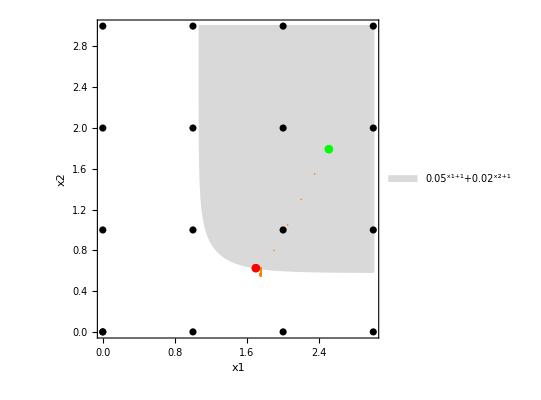

```mathematica
FindMinSplit[2.5,1.8,λ,ϵ]
```

==Количество итераций34033

Исходный резерв:

== процессорного блока++12

== цифро-аналогового блока++12

Необходимое изменение резерва:

== процессорного блока-0.712769

== цифро-аналогового блока-1.21926

Итоговый резерв:

== процессорного блока→→1.287232

== цифро-аналогового блока→→0.7807441

==Вероятность отказа системы0.000525

==Потребляемая мощность системы19

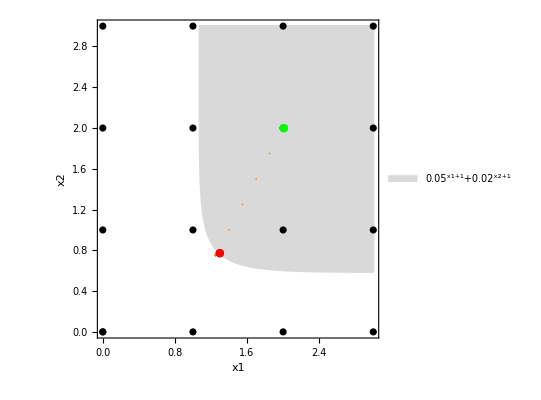

```mathematica
FindMinSplit[2,2,λ,ϵ]
```

==Количество итераций105810

Исходный резерв:

== процессорного блока++12

== цифро-аналогового блока++11

Необходимое изменение резерва:

== процессорного блока-0.334182

== цифро-аналогового блока-0.364236

Итоговый резерв:

== процессорного блока→→1.665822

== цифро-аналогового блока→→0.6357641

==Вероятность отказа системы0.000525

==Потребляемая мощность системы19

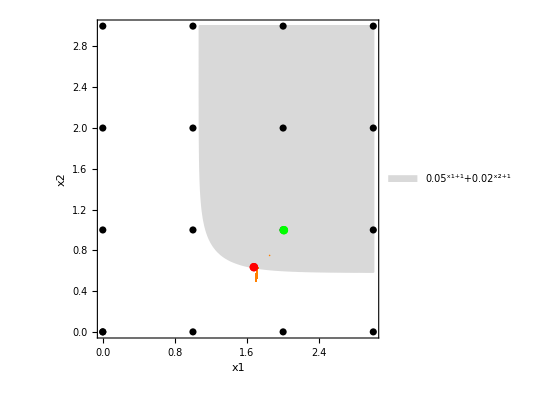

```mathematica
FindMinSplit[2,1,λ,ϵ]
```

#### Старт из области где не выполняется ограничение

==Количество итераций158118

Исходный резерв:

== процессорного блока++10

== цифро-аналогового блока++10

Failed

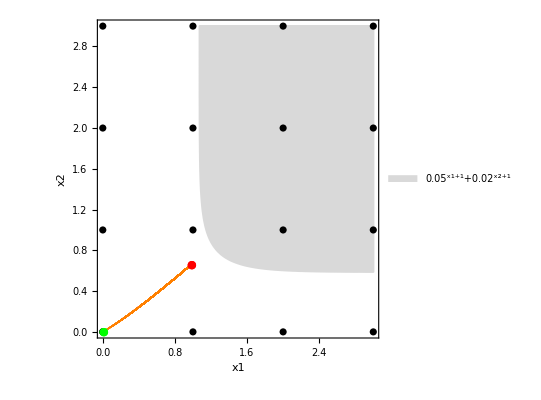

```mathematica
FindMinSplit[0,0,λ,ϵ]
```

==Количество итераций134252

Исходный резерв:

== процессорного блока++12

== цифро-аналогового блока++10

Необходимое изменение резерва:

== процессорного блока-0.00853407

== цифро-аналогового блока0.605335

Итоговый резерв:

== процессорного блока→→1.991472

== цифро-аналогового блока→→0.6053351

==Вероятность отказа системы0.000525

==Потребляемая мощность системы19

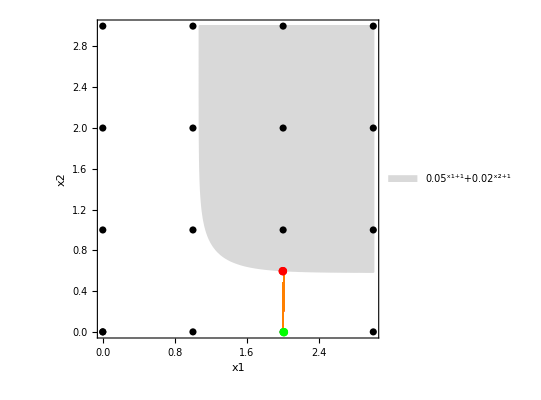

```mathematica
FindMinSplit[2,0,λ,ϵ]
```

==Количество итераций116719

Исходный резерв:

== процессорного блока++11

== цифро-аналогового блока++10

Необходимое изменение резерва:

== процессорного блока0.189841

== цифро-аналогового блока0.623222

Итоговый резерв:

== процессорного блока→→1.189842

== цифро-аналогового блока→→0.6232221

==Вероятность отказа системы0.000525

==Потребляемая мощность системы19

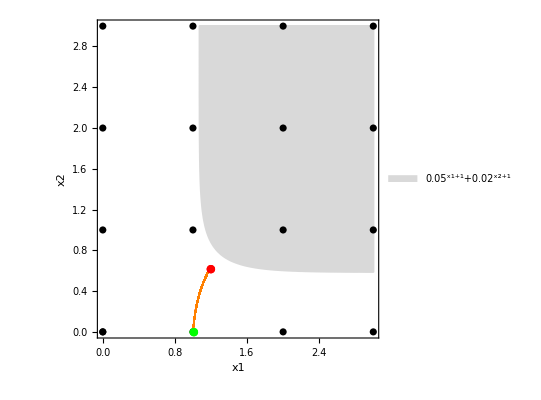

```mathematica
FindMinSplit[1,0,λ,ϵ]
```

Для одного из приведенных примеров (первый из примеров, со стартовой точкой вне ОДР) не удалось найти входящее в ОДР решение. Это связано с тем, что процесс останавливался по величине изменения шага и необходимая точность шага достигалась до нахождения решения.

## Вывод

В лабораторной работе мы познакомились с градиентными методами решения задач нелинейного программирования. В частности, искали оптимальное резерв для блоков ЭВС градиентным методом с дроблением шага. Для чего необходимо было решать задачу в предположении, что количество резервных блоков является непрерывной величиной, а после нахождения решения производился поиск по ближайшим целочисленным значениям.